1+0.0487711 (-1+3 Cos[t]^2)

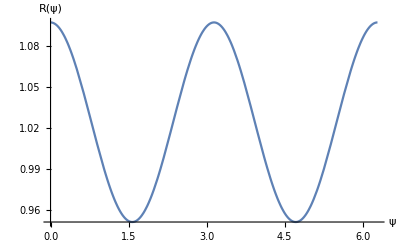

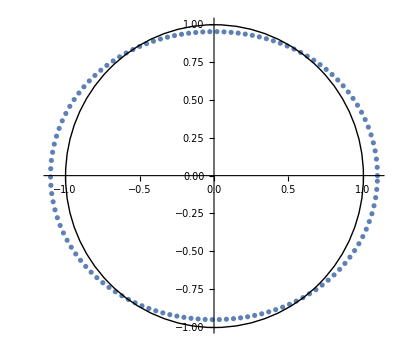

```mathematica
ClearAll["Global`*"]
(* Case 1 : Moon-Earth // Core Density ~= Ocean Density  *)
(* system parameters *)
parA=0.35; a=60.3;
mC=100; mS=1;
zetaC=(mS/mC)*parA*(parA/a)^3;
parB=1; T2=(5/2)*(zetaC/parA);
(* Legendre Polynomial *)
scaleFactor1=1;
scaleFactor2=10^7.3;
p2[t_]=0.5*(3*Cos[t]^2-1);
r[t_]=parB*(1+T2*p2[t]*scaleFactor2)
Plot[r[t],{t,0,2*Pi}, PlotRange->All,AxesLabel->{ψ,R[ψ]}]

(* Initial Solution *)
myList={};
For[i=0, i<2 Pi, i=i+0.05,
xx=r[i]*Cos[i];
yy=r[i]*Sin[i];
AppendTo[myList,{xx,yy}];

]

planetPlot=Graphics[Circle[{0,0},parB]];
bulgePlot=ListPlot[{myList},AspectRatio->Automatic];
Show[{bulgePlot,planetPlot},PlotRange->All,AspectRatio->Automatic]
```

```mathematica
(* Calculate position and rotation for 2 Pi angles *)
bulgeList={};
sateList={};
For[j=0,j<2 Pi,j=j+0.05,
xs=(parB+0.5)*Cos[j];
ys=(parB+0.5)*Sin[j];
tempList={};
For[i=1,i≤ Length[myList],i++,
new=myList[[i]].RotationMatrix[-j];
AppendTo[tempList,new];
]

AppendTo[sateList,{xs,ys}];
AppendTo[bulgeList,tempList];
]
```

```mathematica
(* Tidal Bulge - Animation *)
Animate[
lp1=ListPlot[bulgeList[[i]],PlotRange->{{-1.6,1.6},{-1.6,1.6}},AspectRatio->Automatic];
lp2=ListPlot[ {{sateList[[i,1]],sateList[[i,2]]}},PlotRange->{{-1.6,1.6},{-1.6,1.6}},AspectRatio->Automatic,PlotStyle->{PointSize[0.03],Red}];
Show[lp1,lp2,planetPlot],{i,1,Length[bulgeList],1},AnimationRate->10]
```